```mathematica
Clear["Global`*"]
PulseList:=PulseHalfList~Join~Rest[Reverse[PulseHalfList]];
PulseNum:=Length[PulseList];
PulsePhaseCorrection[timestep_]:=Piecewise[{PulseList,Table[τ-1≤timestep≤τ,{τ,PulseNum}]}ᵀ];
PulseAmplitude[timestep_]:=√(s/2) Γ Sin[2π 0.5 timestep]^2 Boole[0≤timestep≤PulseNum];
RabiVector[timestep_]:={PulseAmplitude[timestep] Cos[PulsePhaseCorrection[timestep]],PulseAmplitude[timestep] Sin[PulsePhaseCorrection[timestep]],zz};
RabiVectorDisplayed[timestep_]:=1/6 RabiVector[timestep];
StateVector[timestep_]:={x[timestep],y[timestep],z[timestep]};
StateVectorTrajectory[timestep_]:=Flatten[StateVector[timestep]/.StateVectorSolutions⟦1⟧];
StateVectorTrajectory[0]:=-UnitVector[3,3];
```

```mathematica
Γ=0.006 2 π;w=0;
zz=-2π w(*+600 Γ Tanh[-6(t-1)]*)(*+D[ 4 Sin[2π *17t-6Sin[2π 0.5(1/1) t]],t]*);
s=0.45 10^5;
PulseHalfList={0,1}π/2;
(*PulseHalfList={0,11,2}π/6;*)
(*PulseHalfList={0,9,42,11,8,37,2}π/24;*)
StateVectorSolutions=NDSolve[{D[StateVector[timestep],timestep]==RabiVector[timestep]×StateVector[timestep],StateVector[0]==-UnitVector[3,3]},{x,y,z},{timestep,0,PulseNum},MaxSteps->1000000];
StateVectorTrajectory[1]
```

{0.,0.309017,0.951056}

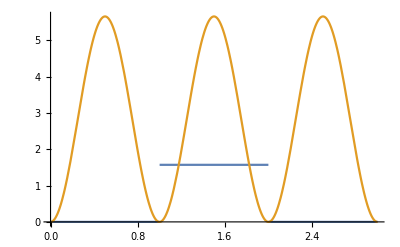

{0.293893,-0.0143841,0.95573}

0.977865

0.022135

```mathematica
Plot[{PulsePhaseCorrection[timestep],PulseAmplitude[timestep]},{timestep,0,Length[PulseList]}]
Animate[Show[Graphics3D[{Opacity[.3],Sphere[{0,0,0}],Point[{0,0,1}]},PlotRange->{{-1.5,1.5},{-1.5,1.5},{-1.5,1.5}},ViewPoint->Above,Boxed->False],ParametricPlot3D[StateVectorTrajectory[τ],{τ,0,PulseNum},PlotPoints->1000],Graphics3D[{Blue,Arrowheads[0.04],Arrow@Tube[{{0,0,0},RabiVectorDisplayed[timestep]},0.01],Red,Arrowheads[0.03],Arrow[Tube[{{0,0,0},StateVectorTrajectory[timestep]},0.01]]}]],{timestep,0,PulseNum}]
StateVectorTrajectory[PulseNum]
(%⟦3⟧+1)/2
(%%⟦3⟧-1)/-2
```

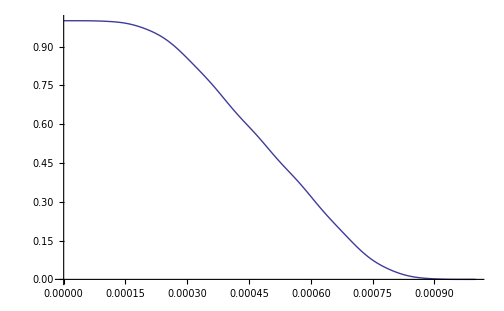

```mathematica
Plot[1-(RR[[1,3]]-1)/-2,{t,0,10^-3},PlotPoints->1000,PlotRange->{0,1}]
```

```mathematica
?Sphere
```

RowBox[{"Sphere", "[", StyleBox["p", "TI"], "]"}] represents a unit sphere centered at the point StyleBox["p", "TI"].
RowBox[{"Sphere", "[", RowBox[{StyleBox["p", "TI"], ",", StyleBox["r", "TI"]}], "]"}] represents a sphere of radius StyleBox["r", "TI"] centered at the point StyleBox["p", "TI"].
RowBox[{"Sphere", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["p", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["p", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["r", "TI"]}], "]"}] represents a collection of spheres of radius StyleBox["r", "TI"].

```mathematica
2π 20. 10^3
1800. Γ
```

125664.

67858.4

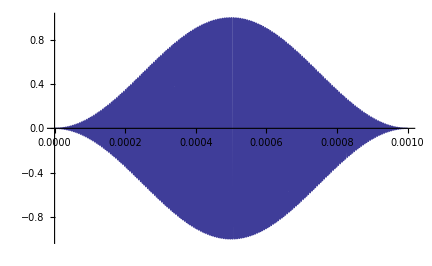

```mathematica
Plot[Sin[2π 0.5 10^3 t]^2 Sin[2π 200 10^3 t],{t,0,10^-3},PlotPoints->2000]
```

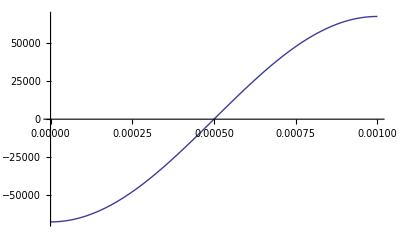

```mathematica
Plot[1800 Γ Sin[2π 10^3(1/2(t1-π/(2π 10^3))+π/(2π 10^3))-π],{t1,0,10^-3}]
```

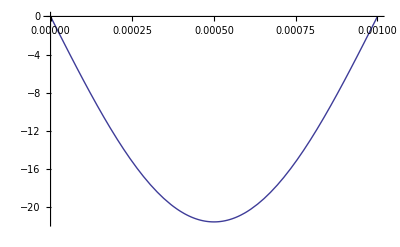

```mathematica
Integrate[1800 Γ Sin[2π 10^3(1/2(t1-π/(2π 10^3))+π/(2π 10^3))-π],{t1,0,t}];
Plot[%,{t,0,10^-3}]
```

```mathematica
ϕ1=Piecewise[{θ1List,Table[i-1≤t≤i,{i,Length[ϕList]}]}ᵀ]//RepeatedTiming
ϕ2=Sum[ϕList⟦τ⟧Boole[τ-1≤t≤τ],{τ,Length[ϕList]}]//RepeatedTiming
```

{0.000011,Piecewise[{{0, 0≤t≤1}, {π/2, 1≤t≤2}, {0, True}}]}

{0.0000138,1/2 π Boole[1≤t≤2]}

```mathematica
ψ1=.;ψ2=.;ψ3=.;
RepeatedTiming[{ψ1=Piecewise[{{√(s/2) Γ Sin[2π 0.5t ]^2,0≤t≤Length[ϕList]}}],PiecewiseExpand[ψ1]}]
RepeatedTiming[{ψ2=√(s/2) Γ Sin[2π 0.5 t]^2 Boole[0≤t≤Length[ϕList]],PiecewiseExpand[ψ2]}]
RepeatedTiming[{ψ3[t_]:=(√(s/2) Γ Sin[2π 0.5 t]^2/;0≤t≤Length[ϕList]),PiecewiseExpand[ψ3]}]
```

{0.00049,{Piecewise[{{6.25169 Sin[3.14159 t]^2, 0≤t≤3}, {0, True}}],Piecewise[{{6.25169 Sin[3.14159 t]^2, 0≤t≤3}, {0, True}}]}}

{0.00049,{6.25169 Boole[0≤t≤3] Sin[3.14159 t]^2,Piecewise[{{0., t>3||t<0}, {6.25169 Sin[3.14159 t]^2, True}}]}}

{6.65×10^-6,{Null,ψ3}}

```mathematica
test[t__]:={Times[Mod[t]],Times[Mod[t]]};
test[2,3]
```

SetDelayed::write: Tag List in {Mod,Mod}[t__] is Protected.

{Mod,Mod}[2,3]